```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
numRAD=7;
epsi=1;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"]
```

{{#,L[fm^-1],C_0[nucl]},{4,-505.15},{6,-1090.55},{8,-1898.55},{10,-2934.2}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTFb=Compile[{{core,_Real,2}},(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2)),{i,Length[core]},{j,Length[core]}]]])^2];

NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2);
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(π^(3/2)/4) Cc/((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2);
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,SinhA,SinhB,SinhC,CoshA,numRAD=radMA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2(1/4)lam^2+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2(1/4)lam^2+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(4 (1./4) lam^2+2 Bb-2 Hh)+Aa (-4 (1/4) lam^2-2 Bb+2 Hh))/(2 (2 (1/4) lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 7 *)
SinhA=If[b1!=0.0&&(Abs[b1 r rp]<Abs[a1 r^2+c1 rp^2]<numRAD),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[b2!=0.0&&(Abs[b2 r rp]<Abs[a2 r^2+c2 rp^2]<numRAD),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[b3!=0.0&&(Abs[b3 r rp]<Abs[a3 r^2+c3 rp^2]<numRAD),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[Abs[b1 r rp]<Abs[a1 r^2+c1 rp^2]<numRAD,Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];
```

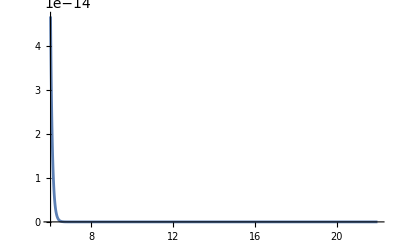

```mathematica
Plot[Exp[-r^2] Sinh[r],{r,numRAD,22},PlotRange->All]
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins"];
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001,numR_]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
(*TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
TanDelSwave*)
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

{0.0501746,0.0513653,0.064451,0.0731739}

{{-2.0832,{{-0.0697933,0.0716},{-0.227882,0.48182},{-0.534121,3.0238},{-0.811119,13.46}}},{-2.03357,{{-0.103955,0.10433},{-0.276233,0.7089},{-0.610448,3.9917},{-0.735012,16.055}}},{-2.05889,{{-0.107949,0.10108},{-0.277929,0.69288},{-0.571938,3.5121},{-0.757802,13.787},{-0.0986155,22.437}}},{-2.02557,{{-0.0653418,0.051875},{-0.270803,0.52526},{-0.360143,2.8672},{-0.183207,3.5017},{-0.87128,13.273}}}}

{B(2) = -2.0832,B(2) = -2.03357,B(2) = -2.05889,B(2) = -2.02557}

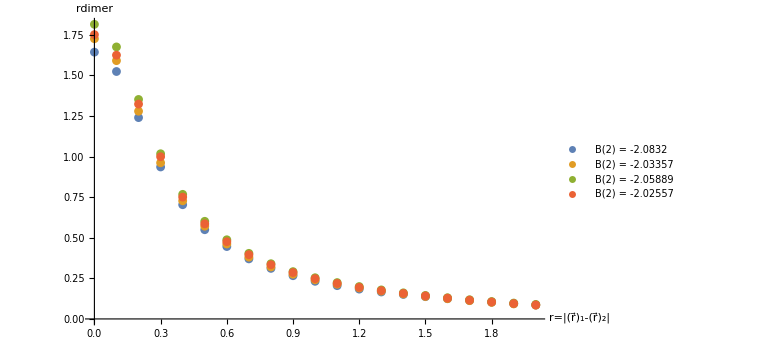

n = 0 terms were excluded from the potentials based on their small contribution.

```mathematica
dCores4={
{-2.08725,{{-0.062870971,0.05093479},{-0.18686446253,0.238419342041},{-0.5732408737,1.363555145263},{-0.79531365775, 7.250524}}},{-2.10116,{{0.148864, 0.087665},{0.385882, 0.61862},{0.570137,2.4742},{0.709844, 7.3577}}},
{-2.08286,{{-0.129864, 0.075504},{-0.426576, 0.56242},{-0.808166, 3.2751},{-0.3607,7.6785},{-0.133911,19.048}}}
};
dCores6={
{-2.08286,{{-0.0698831,0.07160},{-0.227762, 0.48182},{-0.534198,3.0238},{-0.811094, 13.460}}},{-2.03348,{{-0.103955, 0.10433}, {-0.276241, 0.70890}, {-0.610444,3.9917}, {-0.735012, 16.055}}},{-2.05877,{{-0.107951, 0.10108}, {-0.277921, 0.69288}, {-0.571931,3.5121}, {-0.757815, 13.787}, {-0.098584, 22.437}}},{-2.05122,{{-0.0668923,0.051875}, {-0.258185,0.52526}, {-0.484909,2.8672}, {-0.0737611,3.5017}, {-0.829632,13.273}}}
};
dCores8={
{-2.00905,{{0.0768517, 0.087781}, {0.161308, 0.61819}, {0.261105,1.8993}, {0.555285, 7.9488}, {0.769127, 24.796}}},
{-2.01585,{{0.078918, 0.096173}, {0.211313, 0.70364}, {0.292493,3.1413},{0.328697, 7.0005}, {0.869209, 22.774}}},{-2.00429,{{0.0325066, 0.040202}, {0.141497, 0.34418}, {0.156991,1.4974},{0.405265, 4.2883}, {0.888839, 20.981}}},{-2.01356,{{0.0375111, 0.054624}, {0.123751, 0.29495}, {0.251145, 1.5972},{0.586426,6.6529},{0.759151,31.030}}}
};
lambdaTest=6;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
dCores=dCores6;
NormTF[#]&/@dCores[[All,2]]

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]]

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]

cijkl[core_]:=Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]],{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]];
```

{0.000018229,0.0000755486,0.0000511112,0.0000755486,0.0000511112,0.0000755486,0.0000511112,0.0000755486,0.0000511112}

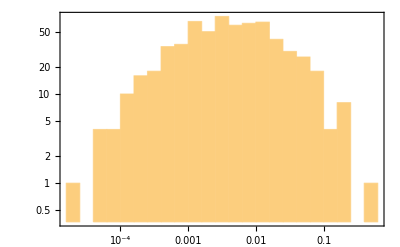

```mathematica
Select[cijkl[dCores[[4]][[2]]],#<10^-4&]
Histogram[cijkl[dCores[[4]][[2]]],"Log","LogCount",Frame->True]
```

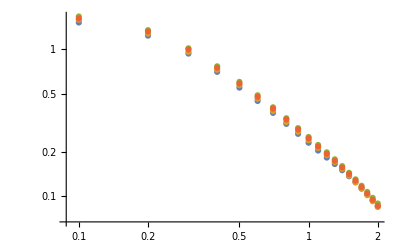

```mathematica
w1=3;w2=4;
ListLogLogPlot[Transpose[{rR,JacobiTrailWavefunctionDataU[[#]]}]&/@Range[Length[dCores]],PlotRange->All]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=6;
grdPerFermi=15;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn,"| maxE=",numRAD," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,{4}(*Length[dCores]*)},{numRAD,Range[1,10]}];
```

finite-difference runtime Δt = 0.102703 mins

core 4| maxE=1 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=1.41736 ; a_dd/a_aa=0.313232

finite-difference runtime Δt = 0.0999691 mins

core 4| maxE=2 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=2.82326 ; a_dd/a_aa=0.623933

finite-difference runtime Δt = 0.100124 mins

core 4| maxE=3 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=3.26815 ; a_dd/a_aa=0.722252

finite-difference runtime Δt = 0.103202 mins

core 4| maxE=4 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=3.56206 ; a_dd/a_aa=0.787205

finite-difference runtime Δt = 0.101724 mins

core 4| maxE=5 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=0.145971 ; a_dd/a_aa=0.0322593

finite-difference runtime Δt = 0.100109 mins

core 4| maxE=6 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=2.78027 ; a_dd/a_aa=0.614432

finite-difference runtime Δt = 0.106521 mins

core 4| maxE=7 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=2.9916 ; a_dd/a_aa=0.661134

finite-difference runtime Δt = 0.111098 mins

core 4| maxE=8 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=3.02352 ; a_dd/a_aa=0.668189

finite-difference runtime Δt = 0.102073 mins

core 4| maxE=9 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=2.90372 ; a_dd/a_aa=0.641714

finite-difference runtime Δt = 0.0991941 mins

core 4| maxE=10 )  λ=6 ; C_0(λ)=-1090.55 ; R_max=6 ; #=90 ; E_match=0.001 ; B(2)=-2.02557 ; dim_d=5 ; a_dd=2.66016 ; a_dd/a_aa=0.587888

```mathematica
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
(* EFT cutoff and energy at which the scattering length is obtained from the amplitude *)
energ=0.01;

(* Integration grid *)
rMa=6.5;
grdPerFermi=10;
nGrd=IntegerPart[rMa grdPerFermi];

(* Plot parameters for the visualization of V(r,r') *)
nR=100;rMi=0.01;thresh=10^-0;

{e0Core,dimerCore}=dCores[[4]];(*ApproxDimerWF[lambd,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];*)

normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Grid[{{"EFT parameters","Numerical parameters","plot control"},{"cutoff regulator λ = "<>ToString[lambdaTest],"R_max = "<>ToString[rMa],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc],"#(Integration grid points) = "<>ToString[nGrd],"plot threshold = "NumberForm[N[thresh]]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All]

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
Grid[{{"Results"},{"a_dd = "<>ToString[tmp],"a_dd/a = "<>ToString[tmp/(hbar/√(Mm Abs[e0Core]))]}},Frame->All]

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potnoloc3d={};
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;
potnoloc3dtmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],mh2 cij WnolocTF3[rR[[i]],rR[[j]],energ,lambdaTest,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2,numRAD]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=thresh,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```

EFT parameters | Numerical parameters | plot control
cutoff regulator λ = 6 | R_max = 6.5 | #(plot grid points) = 100
C_0(λ) = -1090.55 | #(Integration grid points) = 65 | plot threshold =  1.
B(2) = -2.05122 | dimer-basis dimension = 5 |

finite-difference runtime Δt = 0.458862 mins

Results | 
a_dd = 28.3273 | a_dd/a = 6.29976

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

finite-difference runtime Δt = 0.0747023 mins

λ = 6   C_0(λ) = -1090.55     R_max = 3.     #(grid points) = 75                a_dd = 3.04243 fm        a_dd/a_aa = 0.672367

finite-difference runtime Δt = 0.14995 mins

λ = 6   C_0(λ) = -1090.55     R_max = 4.66667     #(grid points) = 116                a_dd = 3.28873 fm        a_dd/a_aa = 0.7268

finite-difference runtime Δt = 0.265931 mins

λ = 6   C_0(λ) = -1090.55     R_max = 6.33333     #(grid points) = 158                a_dd = 2.84756 fm        a_dd/a_aa = 0.629301

finite-difference runtime Δt = 0.421068 mins

λ = 6   C_0(λ) = -1090.55     R_max = 8.     #(grid points) = 200                a_dd = 2.99061 fm        a_dd/a_aa = 0.660917

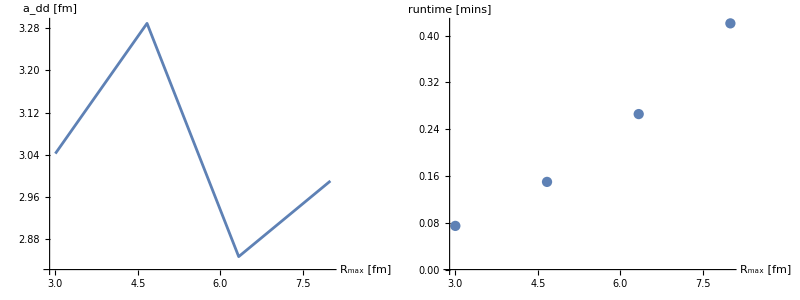

```mathematica
rMaxStart=3;
rMaxEnd=8;
nbrR=3;

coreNBR=4;
{e0Core,dimerCore}=dCores[[coreNBR]];

RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=25;
numRAD=9;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
Wnolo[r_,rp_,Ee_,lam_,Cc_,Aa_,Bb_,Gg_,Hh_,TwoMyOverHBsq_]:=Block[{zeta1,a3,b3,c3,SinhC},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

SinhC=If[b3!=0.0&&(Abs[b3 r rp]<20),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
zeta1 Exp[-a3 r^2-c3 rp^2] SinhC
];
```

```mathematica
coreNBR=3;
rR=Range[0,7,0.1];
{e0Core,dimerCore}=dCores[[coreNBR]];
pl3={};
Do[
ptmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],Wnolo[rR[[i]],rR[[j]],energ,lambdaTest,LECc,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[pl3,ptmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
```

```mathematica
(*potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];*)
p3=Transpose[{pl3[[1]][[All,1]],pl3[[1]][[All,2]],#[[All,3]]}]&/@pl3[[1;;33]];
p4=Transpose[{pl4[[1]][[All,1]],pl4[[1]][[All,2]],#[[All,3]]}]&/@pl4[[1;;33]];
(*ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]*)
Grid[{{ListPlot3D[Re[p3],ImageSize->Large,PlotRange->All],ListPlot3D[Re[p4],ImageSize->Large,PlotRange->All]}}]
```

```mathematica
cijTh=10^-10;
zeta[Aa_,Bb_,Gg_,Hh_,TwoMyOverHBsq_]:=Chop[-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq),cijTh];
a3[lam_,Aa_,Bb_,Gg_,Hh_]:=Chop[(4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh)),cijTh];
b3[lam_,Aa_,Bb_,Gg_,Hh_]:=Chop[(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh)),cijTh];
c3[lam_,Aa_,Bb_,Gg_,Hh_]:=Chop[(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh)),cijTh];
SinhC[r_,rp_,lam_,Cc_,Aa_,Bb_,Gg_,Hh_,TwoMyOverHBsq_]:=Chop[Exp[-a3[lam,Aa,Bb,Gg,Hh] r^2-c3[lam,Aa,Bb,Gg,Hh] rp^2] Sinh[b3[lam,Aa,Bb,Gg,Hh] r rp]/b3[lam,Aa,Bb,Gg,Hh],cijTh];
```

```mathematica
cijTh=10^-3;
coreNBR=4;
{e0Core,dimerCore}=dCores[[coreNBR]];
dimCore=Length[dimerCore];
tmp=Sort[Flatten[ParallelTable[c3[lambdaTest,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]]],{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]]];
ListPlot[tmp,PlotRange->All,ImageSize->Large]
```

```mathematica
SinhC[1.,rp,lambdaTest,LECc,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],mh2]
a3[lambdaTest,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]]]
b3[lambdaTest,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]]]
c3[lambdaTest,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

7.44028

0.

```mathematica
(*cijTh=0.004;
coreNBR=4;
{e0Core,dimerCore}=dCores[[coreNBR]];
setOfIndices=Select[Tuples[Range[Length[dimerCore]],{4}],#[[1]]!=#[[2]]!=#[[3]]!=#[[4]]&];

rp=1.0;
Animate[
Plot[SinhC[r,rp,lambdaTest,LECc,dimerCore[[ii[[1]]]][[2]],dimerCore[[ii[[2]]]][[2]],dimerCore[[ii[[3]]]][[2]],dimerCore[[ii[[4]]]][[2]],mh2],{r,0.1,12.3},PlotRange->All]
,{ii,setOfIndices},AnimationRunning->False
]*)
```